```mathematica
experiments={
"EYrainbow_glucose",
"EYrainbow_glucose_largerBF",
"EYrainbow_rapamycin_1stTry",
"EYrainbow_rapamycin_CheckBistability",
"EYrainbow_1nmpp1_1st",
"EYrainbow_leucine_large",
"EYrainbowWhi5Up_betaEstrodiol"
};
data = Import[FileNameJoin[{NotebookDirectory[],"fitCellSizeWithOrganelle.csv"}],"Data","HeaderLines"->1];
epsilon = 10^(-18);
filled = data/.{0.->epsilon};
washed = Select[data,Function[x,NoneTrue[x,#==0&]]];
```

```mathematica
(* Check data *)
Position[filled,0.]
Position[washed,0.]
```

{}

{}

```mathematica
Length[filled]
Length[washed]
```

43108

29263

```mathematica
fitCellSizeFromOrganelles[dataset_]:=Module[
{expr,a,b,c,alpha,mean,n,nlm,params,fittedFunc,fitted,fittedMin,fittedMax,dataMin,dataMax},
expr = Sum[a[i]n[i]mean[i]^alpha[i],{i,1,6}]+Sum[n[i]mean[i]^alpha[i]b[i,j]n[j]mean[j]^alpha[j],{i,1,6},{j,i,6}]+c;
nlm = NonlinearModelFit[
dataset[[All,2;;]],expr,
Join[
Table[a[i],{i,1,6}],
Flatten[Table[b[i,j],{i,1,6},{j,i,6}]],
{c},
Table[alpha[i],{i,1,6}]
],
Join[
Table[mean[i],{i,1,6}],
Table[n[i],{i,1,6}]
],
MaxIterations->∞
];
params=nlm["BestFitParameters"];
Print["a[i]: ",Table[a[i],{i,1,6}]/.params];
Print["b[i,j]: ",Table[b[i,j],{i,1,6},{j,1,6}]/.params//MatrixForm];
Print["c: ", c/.params];
Print["alpha[i]: ",Table[alpha[i],{i,1,6}]/.params];
Print["Adjusted R Square: ", nlm["AdjustedRSquared"]];
Print["p-values for parameter z-statistics: ", nlm["ParameterPValues"]];
Print["t-statistics for parameter estimates: ", nlm["ParameterTStatistics"]];
fittedFunc = Function[
vec,
expr/.params
/.Table[n[i]->vec[[i]],{i,1,6}]
/.Table[mean[i]->vec[[i+6]],{i,1,6}]
];
fitted = Map[fittedFunc,dataset[[All,2;;-2]]];
fittedMin = Min[fitted];
fittedMax = Max[fitted];
dataMin = Min[dataset[[All,-1]]];
dataMax = Max[dataset[[All,-1]]];
Print[Show[
ListPlot[
Transpose[{dataset[[All,-1]],fitted}],
PlotTheme->"Scientific"
],
Plot[x,{x,0,dataMax}]
]];
Print[""]
]
```

All Experiments, Null Organelles filled with 0:

a[i]: {3.82552,12.6133,-21.9128,0.745641,2.85817,1.59948}

b[i,j]: (0.331175 | -0.58853 | -0.228735 | -0.0597813 | 0.124697 | -0.156068
b$13477[2,1] | 7.49621 | -3.759 | 0.241133 | -0.600461 | 0.530961
b$13477[3,1] | b$13477[3,2] | 3.69175 | -0.380987 | -0.653824 | -0.319836
b$13477[4,1] | b$13477[4,2] | b$13477[4,3] | 0.0123123 | 0.0700795 | 0.171655
b$13477[5,1] | b$13477[5,2] | b$13477[5,3] | b$13477[5,4] | 0.230667 | -0.236894
b$13477[6,1] | b$13477[6,2] | b$13477[6,3] | b$13477[6,4] | b$13477[6,5] | 0.143779)

c: 66.9517

alpha[i]: {0.845372,0.406347,0.666922,1.05675,0.65552,0.829809}

Adjusted R Square: 0.952053

p-values for parameter z-statistics: {4.1067×10^-47,5.42124×10^-71,1.76316×10^-50,0.00510757,8.1361×10^-84,7.31444×10^-13,8.27022×10^-244,8.66504×10^-61,1.37874×10^-12,0.000202402,6.56923×10^-41,2.09893×10^-37,6.83378×10^-151,2.72321×10^-126,1.36841×10^-11,7.73921×10^-163,2.96054×10^-71,1.48586×10^-48,1.26701×10^-23,8.30277×10^-124,3.41354×10^-29,0.000778424,2.40136×10^-11,4.92643×10^-35,0.,7.00941×10^-168,3.41202×10^-97,7.80706×10^-152,0.,0.,0.,2.76327×10^-60,0.,5.26468×10^-308}

t-statistics for parameter estimates: {14.4335,17.8478,-14.9612,2.80031,19.4398,7.17561,33.5628,-16.474,-7.08828,-3.71632,13.4079,-12.793,26.2684,-23.9846,6.76305,-27.3109,17.8818,14.6617,-10.0242,-23.7421,-11.224,3.36059,6.68104,12.3601,47.4687,-27.7396,20.9749,26.3521,77.4041,124.106,93.8101,16.4032,186.16,37.8237}

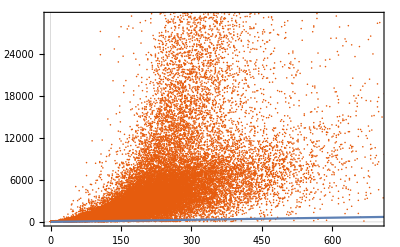

```mathematica
Print["All Experiments, Null Organelles filled with 0:"];
fitCellSizeFromOrganelles[filled];
```

All Experiments, Null Organelles Excluded:

a[i]: {4.15297,13.2552,-0.584623,0.909362,0.70081,0.112199}

b[i,j]: (0.297515 | -0.288189 | -0.0446842 | -0.0207601 | -0.0128407 | -0.120737
b$7382[2,1] | 4.56411 | -1.14714 | 0.0361813 | -0.651291 | 0.598759
b$7382[3,1] | b$7382[3,2] | 0.47419 | -0.102101 | -0.179688 | -0.134486
b$7382[4,1] | b$7382[4,2] | b$7382[4,3] | -0.00547833 | 0.0736075 | 0.0704449
b$7382[5,1] | b$7382[5,2] | b$7382[5,3] | b$7382[5,4] | 0.175173 | -0.145967
b$7382[6,1] | b$7382[6,2] | b$7382[6,3] | b$7382[6,4] | b$7382[6,5] | 0.120232)

c: 18.3037

alpha[i]: {0.890099,0.44813,0.853776,0.97791,0.700691,1.17385}

Adjusted R Square: 0.961846

p-values for parameter z-statistics: {5.29449×10^-65,1.29457×10^-50,0.38475,0.000215802,0.0000191574,0.645137,2.38681×10^-156,1.87664×10^-16,0.00212216,0.22322,0.216512,1.29808×10^-15,1.03055×10^-51,1.85049×10^-25,0.292197,9.65122×10^-121,8.70794×10^-61,8.26972×10^-9,8.17901×10^-9,1.81903×10^-28,2.52533×10^-16,0.214807,1.08534×10^-11,0.0000104926,1.22907×10^-230,1.2997×10^-49,1.06697×10^-46,4.06778×10^-10,0.,0.,0.,7.9002×10^-29,0.,1.68106×10^-173}

t-statistics for parameter estimates: {17.0682,14.9911,-0.86919,3.70023,4.2752,0.460533,26.802,-8.23455,-3.07286,-1.21804,-1.23588,-7.99922,15.1596,-10.4376,1.05333,-23.475,16.486,5.76455,-5.76642,-11.0784,-8.19885,-1.24048,6.79745,4.40753,32.7188,-14.836,14.3753,6.25355,68.9809,87.147,48.9563,11.1532,157.275,28.2715}

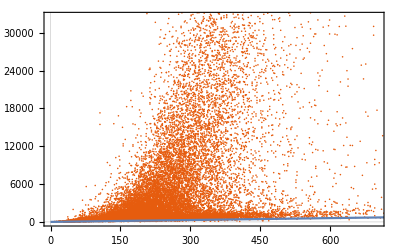

```mathematica
Print["All Experiments, Null Organelles Excluded:"];
fitCellSizeFromOrganelles[washed];
```

EYrainbow_glucose, Null Organelles filled with 0:

a[i]: {2.95191,-2.52228,0.89206,2.12821,3.91563,-0.581085}

b[i,j]: (0.453004 | -1.96067 | -0.17696 | -0.107892 | 0.657511 | -0.162347
b$7863[2,1] | 9.08995 | -0.904763 | 0.624199 | -0.17992 | -0.47797
b$7863[3,1] | b$7863[3,2] | 0.262324 | 0.0178803 | -0.48493 | 0.0574221
b$7863[4,1] | b$7863[4,2] | b$7863[4,3] | 0.0563297 | -0.333532 | -0.0260039
b$7863[5,1] | b$7863[5,2] | b$7863[5,3] | b$7863[5,4] | 0.687624 | -0.308602
b$7863[6,1] | b$7863[6,2] | b$7863[6,3] | b$7863[6,4] | b$7863[6,5] | 0.206513)

c: -5.14084

alpha[i]: {0.687612,0.387199,0.981724,0.531677,0.482259,0.227515}

Adjusted R Square: 0.935182

p-values for parameter z-statistics: {0.00187342,0.255337,0.187043,0.00598929,5.19995×10^-6,0.327975,9.23077×10^-11,7.54135×10^-23,0.00105372,0.213639,4.84452×10^-18,0.00500127,1.22423×10^-19,1.18899×10^-8,0.0000374457,0.12679,2.16823×10^-6,0.00138689,0.609992,7.32582×10^-10,0.0548551,0.269974,1.76045×10^-6,0.569238,1.86662×10^-36,3.00061×10^-9,6.87911×10^-6,0.158091,6.59643×10^-88,0.,2.32397×10^-199,0.00112765,7.24249×10^-299,0.00740225}

t-statistics for parameter estimates: {3.11086,-1.13758,1.31952,2.74926,4.56032,-0.978273,6.48962,-9.87705,-3.27723,-1.24374,8.68199,-2.8079,9.09564,-5.70855,4.12552,-1.52708,-4.74129,3.19873,0.510109,-6.168,1.92036,1.10322,-4.78347,-0.569203,12.6867,-5.93972,4.50102,-1.41168,20.1783,42.5907,31.1936,3.25801,38.9518,2.67902}

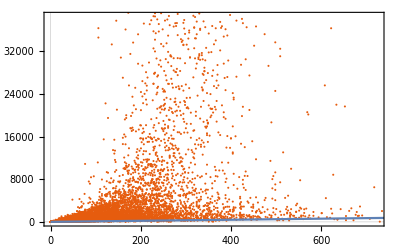

EYrainbow_glucose_largerBF, Null Organelles filled with 0:

a[i]: {13.2167,9.69624,-155.685,-5.5526,7.29337,-4.41846}

b[i,j]: (0.76434 | -0.565969 | -3.26594 | 0.228251 | 0.0315532 | -0.277951
b$8010[2,1] | 9.49365 | -6.39728 | 0.15106 | -1.13657 | 0.300553
b$8010[3,1] | b$8010[3,2] | 57.4694 | -0.0683086 | -2.82388 | 0.779656
b$8010[4,1] | b$8010[4,2] | b$8010[4,3] | 0.302418 | 0.154188 | -0.220426
b$8010[5,1] | b$8010[5,2] | b$8010[5,3] | b$8010[5,4] | 0.193842 | -0.206455
b$8010[6,1] | b$8010[6,2] | b$8010[6,3] | b$8010[6,4] | b$8010[6,5] | 0.16239)

c: 125.895

alpha[i]: {1.0897,0.395254,0.338662,0.734981,0.732091,0.490664}

Adjusted R Square: 0.951318

p-values for parameter z-statistics: {1.61185×10^-8,0.000115889,4.32787×10^-48,0.00114368,3.72474×10^-27,7.28539×10^-6,2.82248×10^-8,0.042325,0.00276553,0.0365817,0.625801,0.0000133157,1.598×10^-18,1.1485×10^-6,0.328971,5.46973×10^-33,0.00113391,2.48987×10^-21,0.932458,1.53114×10^-15,0.0731374,1.44407×10^-10,0.0000435902,5.2757×10^-9,7.07741×10^-52,7.39583×10^-21,2.43215×10^-35,1.17266×10^-121,7.82465×10^-86,3.06751×10^-278,1.61788×10^-134,1.13456×10^-41,0.,1.64025×10^-88}

t-statistics for parameter estimates: {5.65703,3.85723,-14.702,-3.25415,10.8462,-4.48916,5.55954,-2.03075,-2.99392,2.09087,0.487671,-4.35851,8.81146,-4.86937,0.976269,-12.037,3.25659,9.51852,-0.0847565,-7.99609,1.79229,6.42253,4.09062,-5.84685,15.3025,-9.40298,12.4869,24.0087,19.9578,37.6336,25.3297,13.6288,84.3302,20.2843}

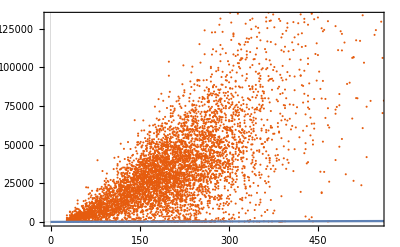

EYrainbow_rapamycin_1stTry, Null Organelles filled with 0:

a[i]: {7.69762,-0.730055,-8.68348,-5.21583,4.12821,-2.84425}

b[i,j]: (0.219516 | -0.630989 | -0.648453 | 0.093569 | 0.0947617 | 0.0528546
b$8156[2,1] | 4.42544 | -1.37357 | 0.902114 | -0.616404 | 0.395749
b$8156[3,1] | b$8156[3,2] | 1.92469 | -0.42829 | -0.317556 | -0.277385
b$8156[4,1] | b$8156[4,2] | b$8156[4,3] | 0.169205 | -0.0392724 | 0.16999
b$8156[5,1] | b$8156[5,2] | b$8156[5,3] | b$8156[5,4] | 0.114097 | -0.01632
b$8156[6,1] | b$8156[6,2] | b$8156[6,3] | b$8156[6,4] | b$8156[6,5] | 0.0588344)

c: 64.152

alpha[i]: {0.609546,0.449023,0.720216,1.60673,0.780768,0.412308}

Adjusted R Square: 0.965942

p-values for parameter z-statistics: {2.13092×10^-16,0.643961,0.00900833,3.77237×10^-11,7.45032×10^-25,9.56345×10^-10,0.00399043,7.37913×10^-8,2.8532×10^-6,0.32368,0.0225676,0.299891,3.05058×10^-13,3.18303×10^-8,7.15044×10^-19,6.70563×10^-33,7.15105×10^-14,0.000697338,0.000246172,1.04937×10^-6,0.0000219781,0.000399024,0.24508,0.0000185383,1.51954×10^-25,0.394616,6.39222×10^-6,3.1332×10^-25,1.67918×10^-29,6.40698×10^-243,3.87491×10^-123,1.33883×10^-53,0.,6.45425×10^-21}

t-statistics for parameter estimates: {8.2345,-0.462188,-2.61246,-6.62328,10.3339,-6.12489,2.87987,-5.38742,-4.68493,0.986993,2.28118,1.03674,7.30621,-5.53727,8.89772,-12.0086,7.50026,3.39213,-3.66809,-4.88646,-4.24665,3.54243,-1.16248,4.28475,10.4876,-0.851328,4.51641,10.4179,11.3299,34.6404,24.0755,15.5446,98.421,9.41207}

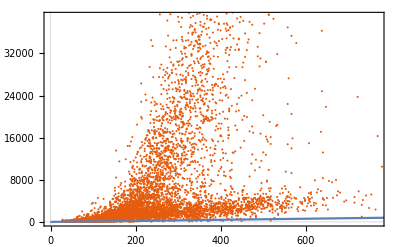

EYrainbow_rapamycin_CheckBistability, Null Organelles filled with 0:

a[i]: {1.5072,-1.29286,2.44348,2.28581,-1.2529,0.163876}

b[i,j]: (0.25552 | -0.269447 | -0.151095 | 0.047614 | 0.124545 | -0.0875568
b$8294[2,1] | 9.66599 | -0.613831 | 0.171577 | -0.318726 | 0.0606784
b$8294[3,1] | b$8294[3,2] | 0.10668 | 0.0321622 | -0.0962549 | 0.00133927
b$8294[4,1] | b$8294[4,2] | b$8294[4,3] | 0.0601688 | -0.194884 | 0.160359
b$8294[5,1] | b$8294[5,2] | b$8294[5,3] | b$8294[5,4] | 0.125102 | -0.139353
b$8294[6,1] | b$8294[6,2] | b$8294[6,3] | b$8294[6,4] | b$8294[6,5] | 0.108846)

c: 34.6499

alpha[i]: {0.925562,0.375567,1.03785,1.18864,0.911968,0.346116}

Adjusted R Square: 0.969927

p-values for parameter z-statistics: {0.0000808941,0.418934,3.04308×10^-53,7.67281×10^-11,1.92105×10^-8,0.580285,2.86524×10^-28,0.00135137,1.13349×10^-10,0.122998,2.42997×10^-14,0.000219035,1.1944×10^-26,3.60352×10^-9,0.0314306,6.78187×10^-15,0.320158,0.000731332,0.0408597,4.37234×10^-11,0.912378,0.0291323,5.19268×10^-22,3.66502×10^-10,1.16002×10^-38,2.78806×10^-26,4.25974×10^-18,2.07488×10^-70,9.50144×10^-266,0.,8.07994×10^-228,3.0986×10^-23,0.,3.73527×10^-13}

t-statistics for parameter estimates: {3.94349,-0.808308,15.4582,6.51446,-5.62389,0.552988,11.0624,-3.20581,-6.45537,1.54245,7.63769,-3.69744,10.7183,-5.90712,2.1519,-7.80141,0.994186,3.37868,2.04524,-6.59876,0.110043,2.18203,-9.66879,6.27446,13.0637,-10.6386,8.68942,17.8911,35.9945,42.2625,33.1455,9.95611,107.232,7.27533}

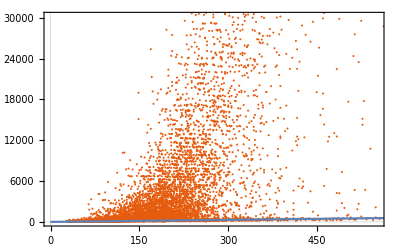

EYrainbow_1nmpp1_1st, Null Organelles filled with 0:

a[i]: {1.11896,0.670299,-2.87073,-0.56777,3.48346,-3.73346}

b[i,j]: (0.0908307 | 0.0032058 | -0.232175 | 0.0456734 | 0.127138 | -0.00440177
b$8432[2,1] | 0.0000630624 | -0.0254336 | 0.0135408 | 0.00537207 | -0.00460567
b$8432[3,1] | b$8432[3,2] | 0.883666 | -0.241032 | -0.520599 | -0.0795162
b$8432[4,1] | b$8432[4,2] | b$8432[4,3] | 0.214296 | -0.00140152 | 0.101649
b$8432[5,1] | b$8432[5,2] | b$8432[5,3] | b$8432[5,4] | 0.105603 | 0.0533672
b$8432[6,1] | b$8432[6,2] | b$8432[6,3] | b$8432[6,4] | b$8432[6,5] | 0.0349469)

c: 27.1398

alpha[i]: {0.664413,1.32993,0.842827,0.460812,0.845939,1.29821}

Adjusted R Square: 0.976786

p-values for parameter z-statistics: {0.0846731,0.00189492,0.0540972,0.326023,6.90464×10^-22,3.60692×10^-15,0.0468717,0.508378,4.82413×10^-6,0.468811,4.65641×10^-6,0.918053,0.510677,0.00566181,0.0199871,0.0332516,0.173341,0.0000253697,9.97052×10^-6,2.66519×10^-17,0.0224405,0.0000105562,0.956034,0.0118322,9.54523×10^-33,0.00301799,0.0690057,1.005×10^-10,7.27915×10^-27,4.75248×10^-58,5.27349×10^-230,2.02001×10^-6,0.,8.36407×10^-52}

t-statistics for parameter estimates: {1.72448,3.1076,-1.92643,-0.982236,9.65256,-7.8885,1.98787,0.661406,-4.57646,0.724462,4.58389,-0.102891,0.657823,-2.76775,2.32721,2.12952,-1.36171,4.21477,-4.42158,-8.48596,-2.28342,4.40919,-0.0551328,2.51788,11.9891,2.96711,1.81871,6.47772,10.783,16.2359,33.845,4.75607,111.744,15.2896}

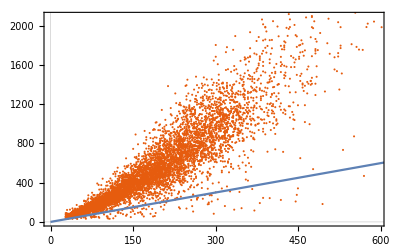

EYrainbow_leucine_large, Null Organelles filled with 0:

a[i]: {0.210138,14.9721,-0.683613,0.258025,0.663041,-4.64271}

b[i,j]: (-0.291243 | -0.414332 | 0.1362 | 0.0255194 | 0.120106 | -0.914814
b$8570[2,1] | 1.81902 | -0.904558 | 0.365765 | -0.273026 | -0.447628
b$8570[3,1] | b$8570[3,2] | 0.407165 | -0.0765402 | -0.0509247 | 0.000528835
b$8570[4,1] | b$8570[4,2] | b$8570[4,3] | 0.0366388 | -0.0679683 | -0.164
b$8570[5,1] | b$8570[5,2] | b$8570[5,3] | b$8570[5,4] | 0.0512271 | 0.378412
b$8570[6,1] | b$8570[6,2] | b$8570[6,3] | b$8570[6,4] | b$8570[6,5] | 0.0736298)

c: 18.4159

alpha[i]: {0.146019,0.525877,0.841906,0.120596,0.804508,2.67003}

Adjusted R Square: 0.973102

p-values for parameter z-statistics: {0.84849,1.83165×10^-14,0.752251,0.618647,0.0461502,0.0359298,7.75377×10^-7,3.69924×10^-6,0.101921,0.611755,0.0000167822,0.00078103,4.40599×10^-13,0.000552855,3.86382×10^-17,2.5736×10^-20,0.00381673,0.072482,0.063485,0.0730168,0.99732,0.00151571,0.0000253278,0.137392,1.07224×10^-14,0.000629974,0.70453,0.0638962,0.0697318,0.,5.96547×10^-56,0.230159,0.,7.97252×10^-15}

t-statistics for parameter estimates: {0.191053,7.68114,-0.315687,0.497795,1.99443,-2.0982,-4.94673,-4.63195,1.63586,0.507597,4.30742,-3.36116,7.25872,-3.45562,8.44237,-9.26889,-2.89406,1.7964,-1.85612,-1.79304,0.00335957,3.17313,-4.21517,-1.48577,7.75011,3.42019,0.379231,1.85325,1.81398,47.4303,15.925,1.20007,78.2084,7.78803}

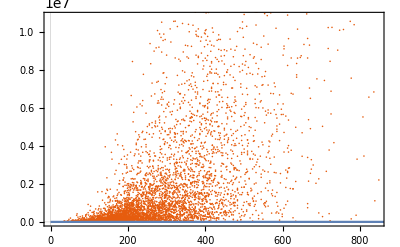

EYrainbowWhi5Up_betaEstrodiol, Null Organelles filled with 0:

a[i]: {4.33854×10^6,-1.00582×10^7,6.22751×10^6,8.86846×10^6,-236196.,-1.11094×10^6}

b[i,j]: (0.624198 | -2.12151 | -4.33853×10^6 | -0.113234 | -0.300917 | -0.698946
b$8708[2,1] | 6.57966 | 1.00582×10^7 | 0.586889 | -0.194036 | 1.16904
b$8708[3,1] | b$8708[3,2] | -6.22762×10^6 | -8.86849×10^6 | 236209. | 1.11093×10^6
b$8708[4,1] | b$8708[4,2] | b$8708[4,3] | 0.213263 | -0.248232 | 0.645248
b$8708[5,1] | b$8708[5,2] | b$8708[5,3] | b$8708[5,4] | 0.0747167 | 0.120053
b$8708[6,1] | b$8708[6,2] | b$8708[6,3] | b$8708[6,4] | b$8708[6,5] | 0.367039)

c: 64.1994

alpha[i]: {0.829483,0.426842,-8.53201×10^-7,1.13622,0.79021,1.24737}

Adjusted R Square: 0.961094

p-values for parameter z-statistics: {0.,0.,0.,0.,0.,0.,8.31424×10^-8,0.0000112899,0.,0.611298,0.000287211,0.000111482,0.00292753,0.,0.225813,0.280167,0.00334947,0.,0.,0.,0.,0.342885,0.0525569,0.0144595,0.00819556,0.220348,0.10844,0.596388,1.1234×10^-82,7.0013×10^-63,2.71965×10^-6,0.0000746437,5.3599×10^-188,1.71428×10^-9}

t-statistics for parameter estimates: {2.66662×10^6,-2.2328×10^6,101883.,2.80673×10^6,-304376.,-741343.,5.40152,-4.41392,-2.66661×10^6,-0.508386,-3.63984,-3.88006,2.98282,2.23281×10^6,1.21199,-1.08055,2.94098,-101885.,-2.80674×10^6,304400.,741337.,0.948945,-1.94092,2.45005,2.64936,1.22639,1.60673,0.529777,21.2656,18.027,-4.71889,3.97808,37.06,6.08114}

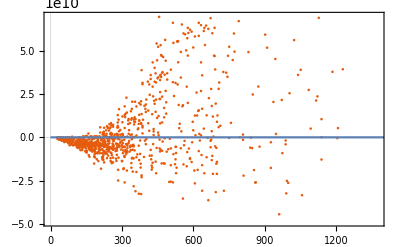

```mathematica
Do[
Print[experiments[[i]],", Null Organelles filled with 0:"];
fitCellSizeFromOrganelles[Select[filled,#[[1]]==experiments[[i]]&]];,
{i,1,Length[experiments]}
];
```

EYrainbow_glucose, Null Organelles Excluded:

a[i]: {5.9464,-3.43527,0.205712,1.24737,1.69065,-0.248826}

b[i,j]: (0.511042 | -1.45354 | -0.177658 | -0.153381 | 0.0879843 | -0.205906
b$9183[2,1] | 12.3106 | -1.8618 | 0.994984 | -0.258158 | -0.719586
b$9183[3,1] | b$9183[3,2] | 0.45797 | 0.0601761 | -0.393475 | 0.129711
b$9183[4,1] | b$9183[4,2] | b$9183[4,3] | 0.141073 | -0.278617 | -0.151978
b$9183[5,1] | b$9183[5,2] | b$9183[5,3] | b$9183[5,4] | 0.471856 | -0.252083
b$9183[6,1] | b$9183[6,2] | b$9183[6,3] | b$9183[6,4] | b$9183[6,5] | 0.240518)

c: -5.3484

alpha[i]: {0.978529,0.370118,0.917038,0.630714,0.570789,0.304559}

Adjusted R Square: 0.949303

p-values for parameter z-statistics: {0.0000171516,0.545372,0.915743,0.328112,0.136203,0.799758,1.1791×10^-7,8.84387×10^-8,0.0681289,0.182064,0.348745,0.0127877,2.36249×10^-8,0.000412205,0.0000752047,0.130147,0.000245786,0.0599449,0.504379,0.000288233,0.0619594,0.0541463,0.00025838,0.0293522,4.08515×10^-13,0.0000671469,0.000512765,0.599901,2.77755×10^-56,3.06108×10^-148,7.68727×10^-58,0.000227539,1.46178×10^-109,0.00744111}

t-statistics for parameter estimates: {4.30488,-0.604767,0.105805,0.978056,1.49041,-0.253679,5.30738,-5.35999,-1.8247,-1.33469,0.937148,-2.49087,5.59558,-3.53544,3.96377,-1.51387,-3.67028,1.88179,0.667683,-3.62921,1.86717,1.92629,-3.65744,-2.17959,7.27972,-3.99084,3.47714,-0.52459,16.0858,27.1875,16.3224,3.69003,23.0239,2.67794}

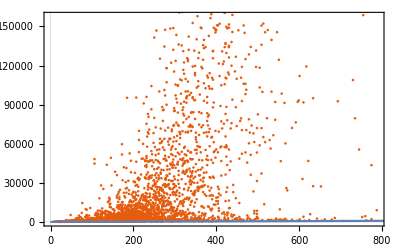

EYrainbow_glucose_largerBF, Null Organelles Excluded:

a[i]: {6.50502,5.24955,3.66289,-4.85324,2.1747,-2.36659}

b[i,j]: (0.278717 | -0.732921 | 0.136386 | 0.105106 | 0.0773574 | -0.291049
b$9321[2,1] | 7.37931 | -0.96354 | 0.175593 | -0.856534 | 0.227435
b$9321[3,1] | b$9321[3,2] | 0.582601 | -0.179207 | -0.365656 | 0.035447
b$9321[4,1] | b$9321[4,2] | b$9321[4,3] | 0.314014 | 0.240474 | -0.233256
b$9321[5,1] | b$9321[5,2] | b$9321[5,3] | b$9321[5,4] | 0.201454 | -0.193498
b$9321[6,1] | b$9321[6,2] | b$9321[6,3] | b$9321[6,4] | b$9321[6,5] | 0.153031)

c: 20.7657

alpha[i]: {1.19524,0.419446,0.831081,0.779214,0.731002,0.467695}

Adjusted R Square: 0.956595

p-values for parameter z-statistics: {0.0000511519,0.139542,0.0051895,2.16391×10^-7,0.00209829,1.06354×10^-6,0.05182,0.0129518,0.383385,0.381819,0.280558,8.48777×10^-6,5.32649×10^-6,0.0365009,0.371156,1.23162×10^-11,0.0157973,0.201495,0.0919342,0.00715184,0.470174,3.98973×10^-8,1.48402×10^-6,6.78482×10^-8,3.18035×10^-39,1.10363×10^-16,3.49773×10^-29,0.00185678,2.62538×10^-62,3.8654×10^-114,1.04592×10^-20,2.871×10^-38,0.,1.33059×10^-71}

t-statistics for parameter estimates: {4.05415,1.47775,2.79637,-5.19258,3.07771,-4.88612,1.94513,-2.48607,0.87176,0.874635,1.07919,-4.45756,4.5569,-2.09192,0.894398,-6.79385,2.41446,1.27749,-1.68564,-2.6909,0.722256,5.50066,4.81973,-5.40567,13.2271,-8.32476,11.2916,3.11405,16.915,23.3621,9.37633,13.0544,68.8614,18.2116}

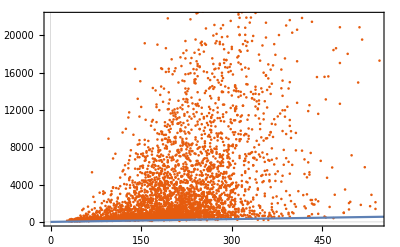

EYrainbow_rapamycin_1stTry, Null Organelles Excluded:

a[i]: {5.82682,4.57242,-18.7452,-4.09339,3.54151,-0.874089}

b[i,j]: (0.189086 | -0.797895 | -0.668507 | 0.107902 | 0.155063 | 0.00449079
b$9467[2,1] | 5.58886 | -2.24923 | 0.82368 | -0.823568 | 0.366606
b$9467[3,1] | b$9467[3,2] | 3.58102 | -0.471294 | -0.416386 | -0.369282
b$9467[4,1] | b$9467[4,2] | b$9467[4,3] | 0.049683 | 0.0058011 | 0.133902
b$9467[5,1] | b$9467[5,2] | b$9467[5,3] | b$9467[5,4] | 0.134734 | -0.00817648
b$9467[6,1] | b$9467[6,2] | b$9467[6,3] | b$9467[6,4] | b$9467[6,5] | 0.0348557)

c: 76.6539

alpha[i]: {0.640333,0.435844,0.654,1.57771,0.750955,0.425658}

Adjusted R Square: 0.974905

p-values for parameter z-statistics: {4.48054×10^-6,0.121052,0.0476276,0.000211732,3.97494×10^-9,0.171361,0.0198538,2.83885×10^-7,0.00214557,0.286048,0.0020132,0.934522,2.35508×10^-7,0.000141712,4.8577×10^-10,3.01989×10^-21,5.73319×10^-7,0.0270586,0.014672,0.000502585,0.00139204,0.351118,0.887758,0.00158507,5.53071×10^-20,0.723784,0.00910717,3.45739×10^-6,3.69337×10^-19,1.28642×10^-135,5.14707×10^-49,4.03074×10^-21,0.,1.91334×10^-8}

t-statistics for parameter estimates: {4.59341,1.55067,-1.98122,-3.70765,5.89699,-1.36806,2.32994,-5.14171,-3.0711,1.06696,3.0901,0.0821618,5.1769,-3.80846,6.2375,-9.51019,5.00728,2.2114,-2.44133,-3.48193,-3.1983,0.93252,0.141149,3.16058,9.19673,-0.353428,2.60914,4.64745,8.9865,25.6641,14.8962,9.4795,72.2855,5.62992}

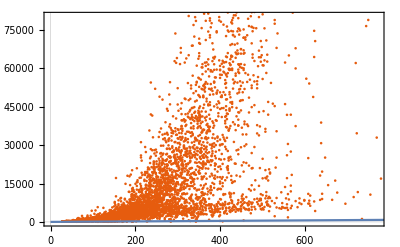

EYrainbow_rapamycin_CheckBistability, Null Organelles Excluded:

a[i]: {1.89571,7.29168,1.76929,3.07509,-0.50279,-0.148195}

b[i,j]: (0.227156 | -0.265587 | -0.110233 | 0.00680404 | 0.073501 | -0.105371
b$9613[2,1] | 9.98781 | -0.908109 | 0.0266606 | -0.387105 | 0.0801424
b$9613[3,1] | b$9613[3,2] | 0.147783 | 0.0641161 | -0.0856065 | 0.0320125
b$9613[4,1] | b$9613[4,2] | b$9613[4,3] | 0.10056 | -0.189433 | 0.123402
b$9613[5,1] | b$9613[5,2] | b$9613[5,3] | b$9613[5,4] | 0.0929538 | -0.0996789
b$9613[6,1] | b$9613[6,2] | b$9613[6,3] | b$9613[6,4] | b$9613[6,5] | 0.075332)

c: 20.949

alpha[i]: {0.934994,0.375421,0.985619,1.25649,0.938131,0.500959}

Adjusted R Square: 0.976605

p-values for parameter z-statistics: {0.000121963,0.0182385,8.33183×10^-6,1.67125×10^-11,0.0292748,0.691831,1.74046×10^-17,0.01666,0.0000551541,0.849669,4.09758×10^-6,0.0000408687,2.22165×10^-7,2.17796×10^-6,0.811997,5.10301×10^-12,0.341138,0.00218466,0.00978776,5.18122×10^-8,0.0805444,0.00152878,3.93136×10^-21,8.6552×10^-6,3.14326×10^-25,1.12541×10^-14,5.51223×10^-8,3.20639×10^-9,1.20733×10^-215,4.97906×10^-113,1.57403×10^-178,5.75688×10^-28,0.,7.52865×10^-10}

t-statistics for parameter estimates: {3.84442,2.36132,4.45996,6.7439,-2.18024,-0.396389,8.53341,-2.39473,-4.03525,0.189548,4.61021,-4.10526,5.18518,-4.74033,0.23786,-6.91529,0.951988,3.0651,2.58398,-5.45124,1.7478,3.17048,-9.46636,4.45177,10.4198,-7.74182,5.44017,5.92868,32.5353,23.0342,29.3803,11.013,93.4268,6.16354}

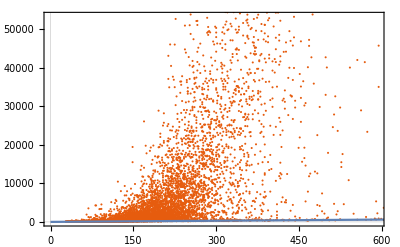

EYrainbow_1nmpp1_1st, Null Organelles Excluded:

a[i]: {-1.15876,0.522812,0.0919175,0.514024,1.52607,-2.12038}

b[i,j]: (-0.0841497 | -0.260237 | 0.0188441 | 0.0566426 | 0.081094 | 0.0529923
b$9751[2,1] | 9.21618 | -1.83955 | 0.72742 | 0.41635 | -0.397742
b$9751[3,1] | b$9751[3,2] | 0.642372 | -0.285608 | -0.401078 | -0.0402345
b$9751[4,1] | b$9751[4,2] | b$9751[4,3] | 0.139554 | 0.040592 | 0.041029
b$9751[5,1] | b$9751[5,2] | b$9751[5,3] | b$9751[5,4] | 0.093531 | 0.0342095
b$9751[6,1] | b$9751[6,2] | b$9751[6,3] | b$9751[6,4] | b$9751[6,5] | 0.0108732)

c: 24.7762

alpha[i]: {0.565076,0.387141,0.880025,0.349111,0.877316,1.49251}

Adjusted R Square: 0.980977

p-values for parameter z-statistics: {0.174974,0.896984,0.950659,0.464412,0.000691701,0.0000442737,0.125635,0.299051,0.728908,0.367239,0.00437862,0.237408,0.000120683,6.05458×10^-7,0.00173526,3.79447×10^-6,0.0114727,0.00253375,0.0000193825,8.07763×10^-10,0.193448,0.00132656,0.0803604,0.279261,8.88357×10^-28,0.0392181,0.570808,1.59495×10^-6,1.79955×10^-15,2.35169×10^-55,1.50317×10^-136,0.00247548,0.,7.38078×10^-26}

t-statistics for parameter estimates: {-1.35661,0.12948,0.0618821,0.731663,3.3952,-4.08798,-1.53183,-1.03859,0.3466,0.901749,2.85096,1.18165,3.8481,-4.99665,3.13404,4.62808,-2.529,3.02098,-4.27645,-6.15663,-1.30064,3.21219,1.74899,1.08211,10.997,2.06249,0.566904,4.80536,7.98289,15.8889,25.7521,3.02803,112.095,10.5803}

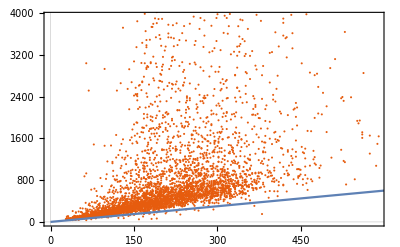

EYrainbow_leucine_large, Null Organelles Excluded:

a[i]: {5.31113,13.8949,0.870391,0.913158,-2.03095,3.69577}

b[i,j]: (-0.307349 | -0.318516 | -0.0536264 | 0.226878 | -0.080775 | 0.308196
b$9889[2,1] | 1.88546 | -0.596877 | 0.219731 | -0.344273 | -0.290226
b$9889[3,1] | b$9889[3,2] | 0.250487 | -0.00333324 | -0.0453576 | -0.0118978
b$9889[4,1] | b$9889[4,2] | b$9889[4,3] | -0.00477803 | -0.0941173 | -0.0353931
b$9889[5,1] | b$9889[5,2] | b$9889[5,3] | b$9889[5,4] | 0.103132 | 0.0713563
b$9889[6,1] | b$9889[6,2] | b$9889[6,3] | b$9889[6,4] | b$9889[6,5] | -0.107345)

c: 19.8813

alpha[i]: {0.396596,0.526502,0.88102,-0.204324,0.784617,0.926782}

Adjusted R Square: 0.974764

p-values for parameter z-statistics: {0.0000495185,3.85723×10^-8,0.70071,0.132654,0.000178629,0.00114576,0.0000647963,0.0039561,0.491882,0.000155244,0.111717,0.00538873,2.82411×10^-8,0.0399598,5.68287×10^-7,5.55588×10^-14,0.0000532546,0.292113,0.928385,0.263336,0.867847,0.725981,0.0000364611,0.410927,1.13653×10^-10,0.0931536,0.0850725,0.144721,0.0000330528,7.81381×10^-262,3.87039×10^-23,0.0788341,0.,6.60333×10^-12}

t-statistics for parameter estimates: {4.06199,5.50721,0.384387,1.504,-3.75073,3.25423,-3.99855,-2.88319,-0.687377,3.78588,-1.59085,2.78424,5.56224,-2.05479,5.00923,-7.54324,-4.04492,1.05363,-0.0898817,-1.11869,-0.166403,-0.3505,-4.13315,-0.822343,6.46349,1.67936,-1.72238,1.4587,4.15573,37.1031,9.96439,-1.75791,64.1529,6.88516}

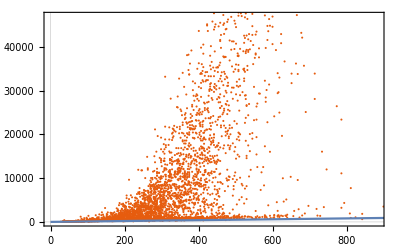

EYrainbowWhi5Up_betaEstrodiol, Null Organelles Excluded:

a[i]: {7.68157,11.7629,-0.471,0.661684,11.0869,-10.567}

b[i,j]: (0.353407 | -0.701833 | 0.0486934 | -0.598769 | 0.506102 | -1.39214
b$10027[2,1] | 1.26392 | -0.249908 | 0.908802 | -1.05826 | 1.25398
b$10027[3,1] | b$10027[3,2] | 0.0945227 | 0.244717 | -0.11612 | 0.252761
b$10027[4,1] | b$10027[4,2] | b$10027[4,3] | 0.436483 | -1.09812 | 0.702302
b$10027[5,1] | b$10027[5,2] | b$10027[5,3] | b$10027[5,4] | 0.241521 | -0.0921991
b$10027[6,1] | b$10027[6,2] | b$10027[6,3] | b$10027[6,4] | b$10027[6,5] | 0.0193283)

c: -56.1691

alpha[i]: {0.900402,0.562983,0.961984,0.783804,0.727193,1.04914}

Adjusted R Square: 0.965159

p-values for parameter z-statistics: {0.00653947,0.000356344,0.849946,0.87096,3.18954×10^-6,0.00307103,0.00561388,0.0132471,0.673986,0.017676,0.00104488,8.82317×10^-11,0.0820236,0.246047,0.0136508,0.000156951,0.0029197,0.509259,0.296247,0.285531,0.251459,0.0659923,0.000131561,0.00945916,0.0120529,0.591097,0.915295,0.0688801,9.7482×10^-76,1.66696×10^-38,4.11141×10^-11,5.19749×10^-6,4.50906×10^-134,1.27524×10^-16}

t-statistics for parameter estimates: {2.72597,3.58454,-0.189243,0.162487,4.6886,-2.96882,2.7764,-2.48212,0.420825,-2.37684,3.28919,-6.56651,1.74107,-1.16078,2.47132,-3.79638,2.98447,0.660263,1.04514,-1.06863,1.14757,1.84078,-3.84065,2.60074,2.51584,-0.537446,0.106392,-1.82145,20.3604,13.6306,6.68496,4.58514,29.6156,8.44298}

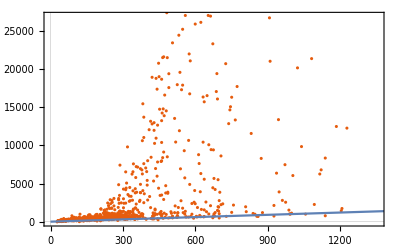

```mathematica
Do[
Print[experiments[[i]],", Null Organelles Excluded:"];
fitCellSizeFromOrganelles[Select[washed,#[[1]]==experiments[[i]]&]];,
{i,1,Length[experiments]}
]
```